# 3. DOMAČA NALOGA

## 1. Naloga

```mathematica
v0={10,3};
GG=9.81;
H=10;
```

X0={0,H}, a={0,-GG}

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Spodnja enačba nam poda položaj “žogice” ob danem času.

```mathematica
X[t_]:=Expand[{0,H}+v0*t+({0,-GG}*t^2)/2]
```

```mathematica
X[2]
```

{20,-3.62}

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Spodnja enačba prikaže vektorsko hitrost ob danem času.

```mathematica
v[t_]:=v0+{0,-GG}*t
```

```mathematica
v[3]
```

{10,-26.43}

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
SlikaTocke[t_]:=Point[X[t]]
```

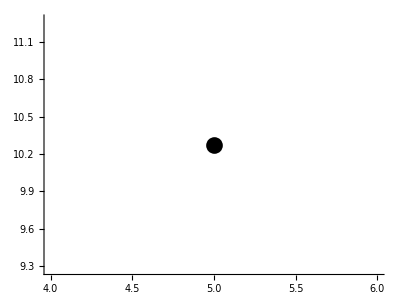

```mathematica
Graphics[{PointSize[0.03],SlikaTocke[0.5]},{Axes->True,AspectRatio->Automatic}]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
PremikVektorja[t_]:={Thickness[Tiny],Arrowheads[0.05],Arrow[{X[t],X[t]+v[t]}]}
```

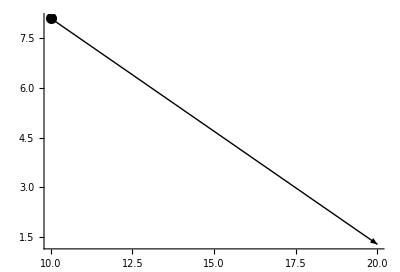

```mathematica
Graphics[{SlikaTocke[1],PremikVektorja[1]},{Axes->True,AspectRatio->Automatic}]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Prikažemo, kje se nahaja žogica po 1 sekundi.

```mathematica
SlikaVektorja[t_]:=Graphics[{PointSize[0.02],SlikaTocke[t],PremikVektorja[t]},Axes->True,PlotRange->{{-1,25},{-5,15}}]
```

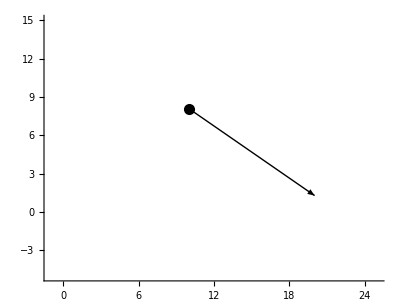

```mathematica
Graphics[SlikaVektorja[1]]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Z uporabo funkcije “Manipulate” animiramo funkcijo “SlikaVektorja”, po zažaljenem časovnem intervalu.

```mathematica
Manipulate[SlikaVektorja[t],{t,0,5}]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Izračunamo čas, ko žogica doseže najvišjo točko in njeno lego (le po y osi) v tem času.

```mathematica
Cas=Solve[v[t][[2]]==0,t]
```

{{t→0.30581}}

```mathematica
t/.Cas
```

{0.30581}

```mathematica
TCas=t/.Cas[[1]]
```

0.30581

```mathematica
X[TCas];
```

```mathematica
NajvišjeTočka=X[TCas][[2]]
```

10.4587

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Izračunamo še čas padca žoge in točko, kjer žoga pade (kjer je y=0)

```mathematica
CasPadca=Solve[X[t][[2]]==0 && t>0,t]
```

{{t→1.76604}}

```mathematica
CasLeta=t/.CasPadca[[1]]
```

1.76604

```mathematica
X[CasLeta];
```

```mathematica
TočkaPadca=X[CasLeta][[1]]
```

17.6604

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Ustvaril sem novo funkcijo “SlikaVektorja2”, kjer sem dodal pridobljene točke in to zavil v funkcijo Manipulate, ki poteka v intervalu od 0 pa do točke padca.

```mathematica
SlikaVektorja2[t_]:=Graphics[{PointSize[0.02],SlikaTocke[t],PremikVektorja[t]},Axes->True,PlotRange->{{-1,TočkaPadca+5},{-1,NajvišjeTočka+5}}]
```

```mathematica
Manipulate[SlikaVektorja2[t],{t,0,CasLeta}]
```

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Absolutna vrednost žogice, ko zadane tla:

```mathematica
AbsolutnaHitrost=(v[CasLeta][[1]]^2+v[CasLeta][[2]]^2)^(1/2)
```

17.47

## 2. Naloga

```mathematica
r111 = Ravnina[{-1,-1,-1},{1,1,1}];
Slika[Ravnina[n_, v_]] :=Hyperplane[n, v]
Format[r_Ravnina] := Graphics3D[Slika[r]]
```

```mathematica
r111
```

-Graphics3D-

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Ustvarimo ravnine, ki gredo skozi točko 0.

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}];
ry=Ravnina[{0, 1, 0}, {0, 0, 0}];
rz=Ravnina[{0, 0, 1}, {0, 0, 0}];
```

```mathematica
ravnine={r111,rx,ry,rz};
```

```mathematica
Graphics3D[Map[{Slika[#],SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
Ustvarimo novo funkcijo, Enacba, ki prikaže enačbo ravnine s podano točko, ki leži v ravnini in njeno normalo.

```mathematica
Enacba[Ravnina[n_,v_]]:=Module[{},
n[[1]]*x+n[[2]]*y+n[[3]]*z==n[[1]]*v[[1]]+n[[2]]*v[[2]]+n[[3]]*v[[3]]
]
```

```mathematica
Enacba[r111]
```

-x-y-z==-3

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
ResiSistem[sistem_List] := Solve[sistem[[1]], sistem[[2]], sistem[[3]], {x, y, z}]
ResiSistem[]
Presecisca[ravnine_List] :=ResiSistem[Map[Subset[Map[Enacba, ravnine], {n}], Enacba]]
```

```mathematica
Vsebuje[Ravnina[n_,v_],x_,y_,z_,eps_:0.000001]:=Module[{tocka},
tocka = {x,y,z};
If[Dot[n, tocka]<eps, True];
If[Dot[n, tocka]>=eps, False]]
```

```mathematica
Trikotnik[r_Ravnina,tocke_List]:= Graphics3D[Map[Line, Subsets[Vsebuje[r, tocke], 2]]]
```

```mathematica
SlikaTrikotnikov[r1_,r2_,r3_,r4_] := Graphics3D[Map[Polygon, Subsets[{r1, r2, r3, r4}], {3}]]
```

```mathematica
SlikaTrikotnikov[r111]
```

SlikaTrikotnikov[-Graphics3D-]

## 3. Naloga

```mathematica
TriPiramida=Tetrahedron[{{3,1,1},{1,3,4},{-1,-1,1},{3,-2,7}}];
```

```mathematica
AA={3,1,1};
BB={1,3,4};
CC={-1,-1,1};
DD={3,-2,7};

VA=BB-AA;
VB=CC-AA;
VC=DD-AA;
```

```mathematica
Produkt[X_,Y_]:=Cross[X,Y]
Razdalja[Vek1_,Vek2_]:=(√(Produkt[Vek1,Vek2].Produkt[Vek1,Vek2]))/2
Razdalja[VA,VB]
```

9

```mathematica
ProstorninaPiramide[VA_,VB_,VC_]:=(Produkt[VA,VB].VC)/6
ProstorninaPiramide[VA,VB,VC]
```

18

```mathematica
Visina[VA_,VB_,VC_]:=Module[{vis,koncna},
vis=(3*ProstorninaPiramide[VA,VB,VC])/Razdalja[VA,VB];
koncna=vis*Produkt[VA,VB]/(Razdalja[VA,VB]*2)
]
vektorVisine=Visina[VA,VB,VC]
```

{2,-4,4}

```mathematica
NN=DD-vektorVisine
```

{1,2,3}

```mathematica
r222=Ravnina[{DD-NN},{NN}];
NormalAA=Cross[VA,VB]
```

{6,-12,12}

```mathematica
n=Arrow[{NN,NN+NormalAA/2}]
```

Arrow[{{1,2,3},{4,-4,9}}]

```mathematica
Graphics3D[{n,{Opacity[0.3],LightBlue,TriPiramida},{PointSize[Large],Red,Point[NN]},{Red,Line[{NN,DD}]}},Axes->True]
```

-Graphics3D-

Višina tristranične piramide, je normala.